```mathematica
Needs["ExperimentEvaluation`"]
```

```mathematica
labels=Flatten[Outer[StringJoin,{"GP_","GPAT_","GPAT_GP_"},{"52","53","55","60","65","70","90"}]]
```

{GP_52,GP_53,GP_55,GP_60,GP_65,GP_70,GP_90,GPAT_52,GPAT_53,GPAT_55,GPAT_60,GPAT_65,GPAT_70,GPAT_90,GPAT_GP_52,GPAT_GP_53,GPAT_GP_55,GPAT_GP_60,GPAT_GP_65,GPAT_GP_70,GPAT_GP_90}

```mathematica
data=readAllFiles[{"20110803/GP4D_1000","GPAT4D_SSM_500"},labels,ReplaceParamValues->{"FC55"->"ZFC55"}];
```

```mathematica
data=readAllFiles[{"GP_MAZE_1000","GPAT_MAZE_1000","GPAT_MAZE_1000_GP"},labels];
```

```mathematica
names=Flatten@Transpose@{{"GP_MAZE_MAP2_ORIG","GP_MAZE_MAP2_RF4","GP_MAZE_MAP2_RF8","GP_MAZE_MAP2_NOVER","GP_MAZE_MAP3_ORIG","GP_MAZE_MAP3_RF4","GP_MAZE_MAP3_RF8","GP_MAZE_MAP3_NOVER"},{"GPAT_MAZE_MAP2_ORIG","GPAT_MAZE_MAP2_RF4","GPAT_MAZE_MAP2_RF8","GPAT_MAZE_MAP2_NOVER","GPAT_MAZE_MAP3_ORIG","GPAT_MAZE_MAP3_RF4","GPAT_MAZE_MAP3_RF8","GPAT_MAZE_MAP3_NOVER"}};
```

```mathematica
labels=Flatten@Transpose@{{"GP_MAP2_ORIG","GP_MAP2_RF4","GP_MAP2_RF8","GP_MAP2_NOVER","GP_MAP3_ORIG","GP_MAP3_RF4","GP_MAP3_RF8","GP_MAP3_NOVER"},{"GPAT_MAP2_ORIG","GPAT_MAP2_RF4","GPAT_MAP2_RF8","GPAT_MAP2_NOVER","GPAT_MAP3_ORIG","GPAT_MAP3_RF4","GPAT_MAP3_RF8","GPAT_MAP3_NOVER"}};
```

```mathematica
data=readAllFiles[names,labels];
```

```mathematica
keepOnlyBest[{"GPAT_MAZE_MAP2_ORIG","GPAT_MAZE_MAP2_RF4","GPAT_MAZE_MAP2_RF8"},"BSF",5]
```

```mathematica
changingParameters[data]
```

{GPAT.FUNCTION_IMPL,GP.MAX_EVALUATIONS,GP.MUTATION_CAUCHY_PROBABILITY,GP.TYPE,MAZE.MAX_STEPS,SOLVER}

```mathematica
sortedData = data;
```

```mathematica
sortedData=sortDataByParams[data,{"MAZE.MAX_STEPS","SYMBOLIC_REGRESSION_1D.F","SYMBOLIC_REGRESSION_1D.A","SOLVER","GPAT.SPECIES_SIZE_MEAN"},ReplaceParamValues->{"ZFC55"->"FC55"}];
```

```mathematica
saveData[sortedData,"GP3D_H_H2_200"]
```

```mathematica
printAsTable[sortedData,{"SOLVER","MAZE.MAX_STEPS","SYMBOLIC_REGRESSION_1D.A","SYMBOLIC_REGRESSION_3D.F","GPAT.SPECIES_SIZE_MEAN"}]
```

ID | PARAM FILE | SOLVER | MAZE.MAX_STEPS | SYMBOLIC_REGRESSION_1D.A | SYMBOLIC_REGRESSION_3D.F | GPAT.SPECIES_SIZE_MEAN
GP_MAP2_ORIG | GP_MAZE_MAP2_ORIG/parameters_001.txt | GP | 90 | NONE | NONE | NONE
GPAT_MAP2_ORIG | GPAT_MAZE_MAP2_ORIG/parameters_001.txt | GPAT | 90 | NONE | NONE | 20.
GP_MAP2_RF4 | GP_MAZE_MAP2_RF4/parameters_001.txt | GP | 90 | NONE | NONE | NONE
GPAT_MAP2_RF4 | GPAT_MAZE_MAP2_RF4/parameters_001.txt | GPAT | 90 | NONE | NONE | 20.
GP_MAP2_RF8 | GP_MAZE_MAP2_RF8/parameters_001.txt | GP | 90 | NONE | NONE | NONE
GPAT_MAP2_RF8 | GPAT_MAZE_MAP2_RF8/parameters_001.txt | GPAT | 90 | NONE | NONE | 20.
GP_MAP2_NOVER | GP_MAZE_MAP2_NOVER/parameters_001.txt | GP | 90 | NONE | NONE | NONE
GPAT_MAP2_NOVER | GPAT_MAZE_MAP2_NOVER/parameters_001.txt | GPAT | 90 | NONE | NONE | 20.
GP_MAP3_ORIG | GP_MAZE_MAP3_ORIG/parameters_001.txt | GP | 90 | NONE | NONE | NONE
GPAT_MAP3_ORIG | GPAT_MAZE_MAP3_ORIG/parameters_001.txt | GPAT | 90 | NONE | NONE | 20.
GP_MAP3_RF4 | GP_MAZE_MAP3_RF4/parameters_001.txt | GP | 90 | NONE | NONE | NONE
GPAT_MAP3_RF4 | GPAT_MAZE_MAP3_RF4/parameters_001.txt | GPAT | 90 | NONE | NONE | 20.
GP_MAP3_RF8 | GP_MAZE_MAP3_RF8/parameters_001.txt | GP | 90 | NONE | NONE | NONE
GPAT_MAP3_RF8 | GPAT_MAZE_MAP3_RF8/parameters_001.txt | GPAT | 90 | NONE | NONE | 20.
GP_MAP3_NOVER | GP_MAZE_MAP3_NOVER/parameters_001.txt | GP | 90 | NONE | NONE | NONE
GPAT_MAP3_NOVER | GPAT_MAZE_MAP3_NOVER/parameters_001.txt | GPAT | 90 | NONE | NONE | 20.

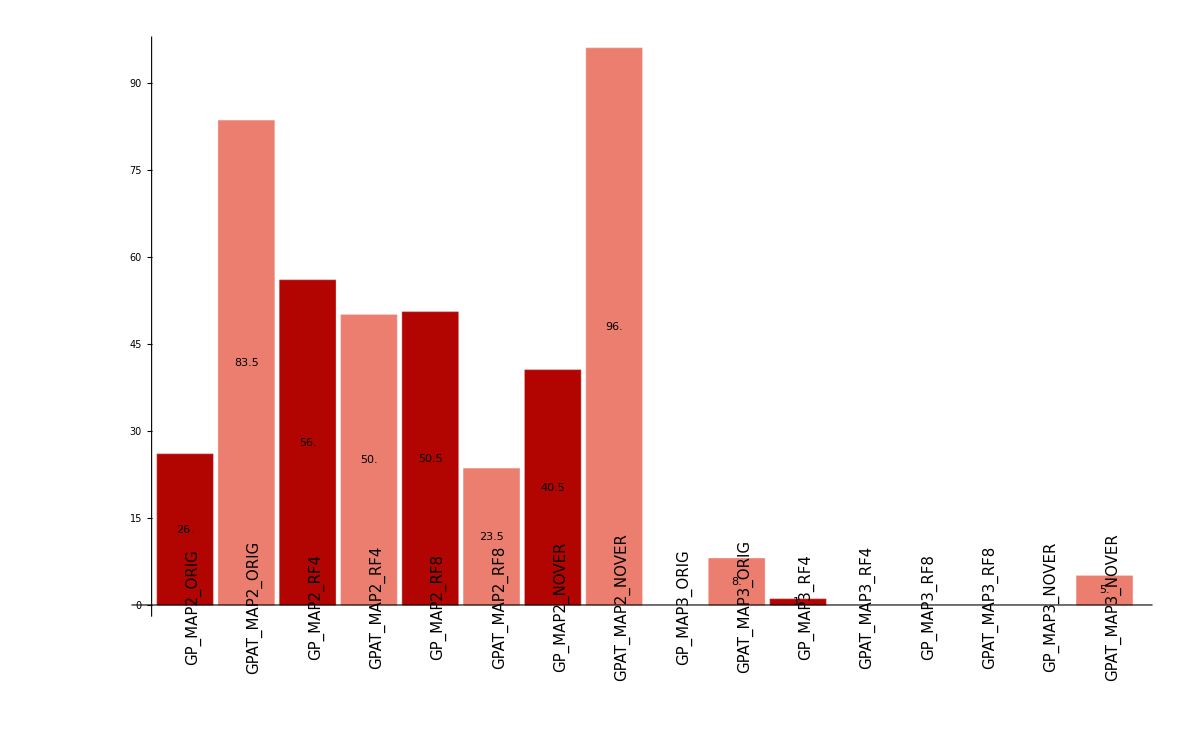

```mathematica
plotBooleanAsBarChart[sortedData,"SUCCESS",2]
```

```mathematica
plotAsBoxWhiskerChart[sortedData,"BSF"];
```

```mathematica
testMannWhitney[data,"GPAT_H","GPAT_H2","BSF"]
```

median 1: 0.952853

median 2: 0.949325

mean 1: 0.754262

mean 2: 0.528663

variance 1: 0.135817

variance 2: 0.222969

higher/lower variance ratio: 1.64169

U stat: 22636

P-value: 0.0226329

The null hypothesis that the median difference is 0 is rejected at the 5. percent level based on the Mann-Whitney test.

```mathematica
testKruskalWallis[data,{"GP_H","GPAT_H2"},"BSF"]
```

| GPAT_H | GPAT_H2
Mean | 0.754262 | 0.528663
Variance | 0.952853 | 0.949325
Variance | 0.135817 | 0.222969

LocationEquivalenceTest::ntsymmd: The p-value in 1.14305×10^-13, resulting from a test for symmetry, is below 0.05. The tests in {"KruskalWallis"} require that the data is symmetric about a common median.

| Statistic | P-Value
Kruskal-Wallis | 5.19838 | 0.0224202

```mathematica
testFisherExact[sortedData,"GPAT_MAP2_RF4","GP_MAP2_NOVER","SUCCESS",TwoSided->True,PValueOnly->False]
```

| GPAT_MAP2_RF4 | GP_MAP2_NOVER
true | 100. | 81.
false | 100. | 119.

0.0704417

```mathematica
testFisherExactAll[data,"SUCCESS",0.05,TwoSided->True]
```

| GPAT_MAP2_ORIG | GP_MAP2_RF4 | GPAT_MAP2_RF4 | GP_MAP2_RF8 | GPAT_MAP2_RF8 | GP_MAP2_NOVER | GPAT_MAP2_NOVER | GP_MAP3_ORIG | GPAT_MAP3_ORIG | GP_MAP3_RF4 | GPAT_MAP3_RF4 | GP_MAP3_RF8 | GPAT_MAP3_RF8 | GP_MAP3_NOVER | GPAT_MAP3_NOVER
GP_MAP2_ORIG | 2.9235×10^-32 | 1.45139×10^-9 | 1.11279×10^-6 | 6.73151×10^-7 | 0.643185 | 0.0028909 | 7.01904×10^-53 | 9.74921×10^-18 | 2.03328×10^-6 | 4.72895×10^-15 | 9.74921×10^-18 | 9.74921×10^-18 | 9.74921×10^-18 | 9.74921×10^-18 | 4.35966×10^-9
GPAT_MAP2_ORIG |  | 2.60195×10^-9 | 1.07623×10^-12 | 2.15731×10^-12 | 5.04552×10^-35 | 3.61018×10^-19 | 0.0000478615 | 2.74826×10^-79 | 8.54885×10^-58 | 2.87819×10^-75 | 2.74826×10^-79 | 2.74826×10^-79 | 2.74826×10^-79 | 2.74826×10^-79 | 3.74581×10^-64
GP_MAP2_RF4 |  |  | 0.270448 | 0.316287 | 3.85698×10^-11 | 0.00263922 | 9.93176×10^-23 | 9.55738×10^-44 | 2.30899×10^-26 | 2.98744×10^-40 | 9.55738×10^-44 | 9.55738×10^-44 | 9.55738×10^-44 | 9.55738×10^-44 | 3.3368×10^-31
GPAT_MAP2_RF4 |  |  |  | 1. | 5.45954×10^-8 | 0.0704417 | 1.10289×10^-27 | 8.078×10^-38 | 1.89489×10^-21 | 1.86469×10^-34 | 8.078×10^-38 | 8.078×10^-38 | 8.078×10^-38 | 8.078×10^-38 | 6.41276×10^-26
GP_MAP2_RF8 |  |  |  |  | 3.1367×10^-8 | 0.0562851 | 2.965×10^-27 | 2.69267×10^-38 | 7.71512×10^-22 | 6.38001×10^-35 | 2.69267×10^-38 | 2.69267×10^-38 | 2.69267×10^-38 | 2.69267×10^-38 | 2.42766×10^-26
GPAT_MAP2_RF8 |  |  |  |  |  | 0.000383781 | 3.40826×10^-56 | 6.61756×10^-16 | 0.000028434 | 2.5738×10^-13 | 6.61756×10^-16 | 6.61756×10^-16 | 6.61756×10^-16 | 6.61756×10^-16 | 1.05276×10^-7
GP_MAP2_NOVER |  |  |  |  |  |  | 1.74485×10^-36 | 2.92199×10^-29 | 1.19348×10^-14 | 3.95857×10^-26 | 2.92199×10^-29 | 2.92199×10^-29 | 2.92199×10^-29 | 2.92199×10^-29 | 1.74832×10^-18
GPAT_MAP2_NOVER |  |  |  |  |  |  |  | 1.47299×10^-105 | 2.50057×10^-82 | 2.55012×10^-101 | 1.47299×10^-105 | 1.47299×10^-105 | 1.47299×10^-105 | 1.47299×10^-105 | 2.45686×10^-89
GP_MAP3_ORIG |  |  |  |  |  |  |  |  | 0.0000223343 | 0.498747 | 1. | 1. | 1. | 1. | 0.00174052
GPAT_MAP3_ORIG |  |  |  |  |  |  |  |  |  | 0.00103044 | 0.0000223343 | 0.0000223343 | 0.0000223343 | 0.0000223343 | 0.310577
GP_MAP3_RF4 |  |  |  |  |  |  |  |  |  |  | 0.498747 | 0.498747 | 0.498747 | 0.498747 | 0.0357799
GPAT_MAP3_RF4 |  |  |  |  |  |  |  |  |  |  |  | 1. | 1. | 1. | 0.00174052
GP_MAP3_RF8 |  |  |  |  |  |  |  |  |  |  |  |  | 1. | 1. | 0.00174052
GPAT_MAP3_RF8 |  |  |  |  |  |  |  |  |  |  |  |  |  | 1. | 0.00174052
GP_MAP3_NOVER |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 0.00174052

```mathematica
sortConfigurationResults[sortedData,"A","BSF",10]
```

1 | 0.996687
12 | 0.983575
100 | 0.970368
78 | 0.96933
10 | 0.968461
60 | 0.968217
79 | 0.963918
73 | 0.958339
68 | 0.956159
35 | 0.955737

```mathematica
Expand[1.5*x1*x2+2.3*x1+x2*x3*x4-1.1*x3]
```

2.3 x1+1.5 x1 x2-1.1 x3+x2 x3 x4

```mathematica
(res=sortConfigurationResults[sortedData,"GP3D_H2","BSF",10,Output->"Expressions"]/.{x0->Subscript[x, 1],x1->Subscript[x, 2],x2->Subscript[x, 3],x3->Subscript[x, 4]})
```

Gen | Expression | Expanded | f
last | {x_2 (-1.+x_1 (x_3+x_2 x_3))} | {-1. x_2+x_1 x_2 x_3+x_1 x_2^2 x_3} | 1.
last | {x_2 (-1.+x_1 x_3+x_1 x_2 x_3)} | {-1. x_2+x_1 x_2 x_3+x_1 x_2^2 x_3} | 1.
last | {-1. x_2+(x_1 x_2+x_1 x_2^2) x_3} | {-1. x_2+x_1 x_2 x_3+x_1 x_2^2 x_3} | 1.
last | {-1. x_2+x_1 x_2 x_3+x_1 x_2^2 x_3} | {-1. x_2+x_1 x_2 x_3+x_1 x_2^2 x_3} | 1.
last | {-1. x_2+x_2 (x_1+x_1 x_2) x_3} | {-1. x_2+x_1 x_2 x_3+x_1 x_2^2 x_3} | 1.
last | {x_1 x_2^2 x_3+x_2 (-1.+x_1 x_3)} | {-1. x_2+x_1 x_2 x_3+x_1 x_2^2 x_3} | 1.
last | {x_1-1. x_2+x_1 (-1.+x_2 x_3+x_2^2 x_3)} | {0.-1. x_2+x_1 x_2 x_3+x_1 x_2^2 x_3} | 1.
last | {x_2 (-1.+(x_1+x_1 x_2) x_3)} | {-1. x_2+x_1 x_2 x_3+x_1 x_2^2 x_3} | 1.
last | {1.08185×10^-8-1. x_2+(x_1 x_2+x_1 x_2^2) x_3} | {1.08185×10^-8-1. x_2+x_1 x_2 x_3+x_1 x_2^2 x_3} | 1.
last | {-1. x_2+x_1 (4.44373×10^-11+x_2 x_3+x_2^2 x_3)} | {4.44373×10^-11 x_1-1. x_2+x_1 x_2 x_3+x_1 x_2^2 x_3} | 1.

```mathematica
(res=sortConfigurationResults[sortedData,"12","BSF",25,Output->"Expressions"]/.{x0->x})
```

Gen | Expression | Expanded | f
last | {0.09977 x (x+Sin[0.787112 ⅇ^(-x^2)])} | {0.09977 x^2+0.09977 x Sin[0.787112 ⅇ^(-x^2)]} | 0.995529
last | {0.0646032 x (ⅇ^(-x^2)+1.55385 x)-0.0344501 Sin[1.-ⅇ^(-x^2)]} | {0.0646032 ⅇ^(-x^2) x+0.100383 x^2-0.0344501 Sin[1.-ⅇ^(-x^2)]} | 0.995316
last | {0.100061 x (0.0156719+x)} | {0.00156814 x+0.100061 x^2} | 0.995278
last | {ⅇ^(-11.8063-Sin[x]^2)+0.0999739 x (0.021377+x)} | {ⅇ^(-11.8063-Sin[x]^2)+0.00213714 x+0.0999739 x^2} | 0.995253
last | {0.100195 x^2} | {0.100195 x^2} | 0.995163
last | {0.0997882 x^2} | {0.0997882 x^2} | 0.995147
last | {-0.0015477+0.100253 x^2} | {-0.0015477+0.100253 x^2} | 0.995127
last | {0.0995871 x^2} | {0.0995871 x^2} | 0.994844
last | {0.0995752 x^2} | {0.0995752 x^2} | 0.99482
last | {0.100443 x^2} | {0.100443 x^2} | 0.994783
last | {0.0999352 (-0.0328145+x) x} | {-0.00327932 x+0.0999352 x^2} | 0.994597
last | {0.0994062 x^2} | {0.0994062 x^2} | 0.994405
last | {0.100651 x^2} | {0.100651 x^2} | 0.994233
last | {4.35401×10^-11+0.100887 x (ⅇ^(-x^2)+x)} | {4.35401×10^-11+0.100887 ⅇ^(-x^2) x+0.100887 x^2} | 0.993847
last | {0.10084 x^2} | {0.10084 x^2} | 0.993554
last | {0.0993273 x (ⅇ^(-33.9284 (3.47822+x)^2)+x)} | {0.0993273 ⅇ^(-33.9284 (3.47822+x)^2) x+0.0993273 x^2} | 0.993273
last | {0.0990122 x^2} | {0.0990122 x^2} | 0.992907
last | {-0.000371379+0.0990141 x^2} | {-0.000371379+0.0990141 x^2} | 0.992889
last | {Sin[0.129682 x] (x-Sin[0.336709 x]-0.196058 Sin[x])} | {x Sin[0.129682 x]-Sin[0.129682 x] Sin[0.336709 x]-0.196058 Sin[0.129682 x] Sin[x]} | 0.992606
last | {0.101464 (-0.763579+x (0.0208029+x))} | {-0.0774756+0.00211074 x+0.101464 x^2} | 0.992428
last | {0.0988539 x^2} | {0.0988539 x^2} | 0.992097
last | {0.101382 x (ⅇ^(-0.332217 x^2)+x)} | {0.101382 ⅇ^(-0.332217 x^2) x+0.101382 x^2} | 0.99195
last | {(0.815193 x^2 (-0.632121 ⅇ^(-(4.80488+x)^2)+x+ⅇ^(-x^2) (2.03518+x)) ArcTan[x])/(√(1+140.445 x^2))} | {(1.65907 ⅇ^(-x^2) x^2 ArcTan[x])/(√(1+140.445 x^2))-(0.5153 ⅇ^(-(4.80488+x)^2) x^2 ArcTan[x])/(√(1+140.445 x^2))+(0.815193 x^3 ArcTan[x])/(√(1+140.445 x^2))+(0.815193 ⅇ^(-x^2) x^3 ArcTan[x])/(√(1+140.445 x^2))} | 0.991336
last | {0.10128 x^2} | {0.10128 x^2} | 0.991321
last | {0.0989743 x (0.0785205+x)} | {0.00777151 x+0.0989743 x^2} | 0.991136

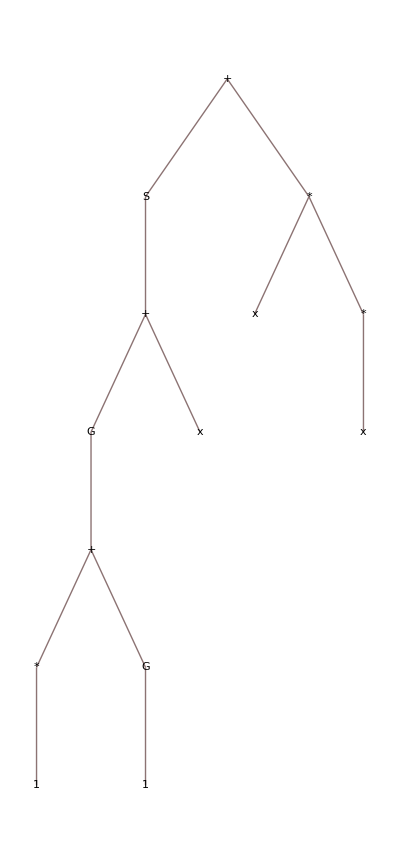
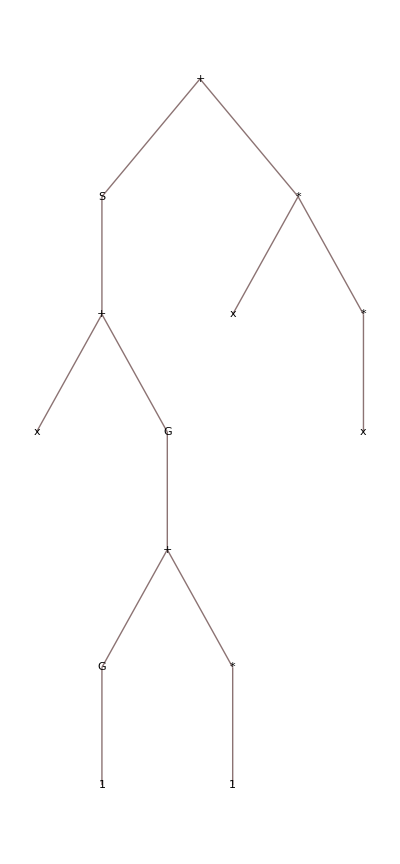
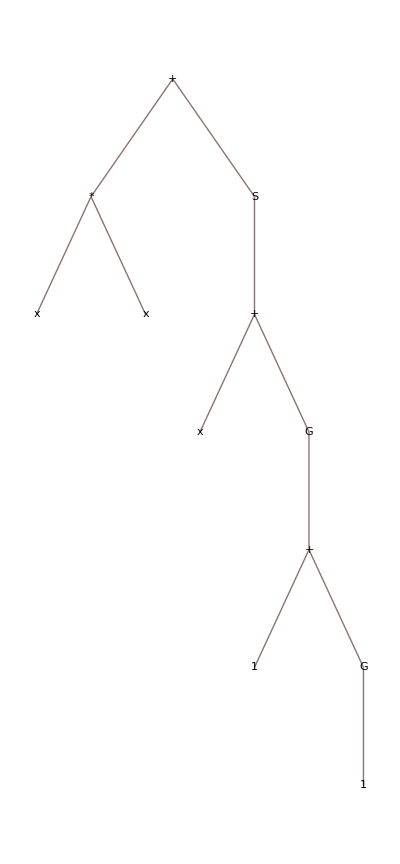
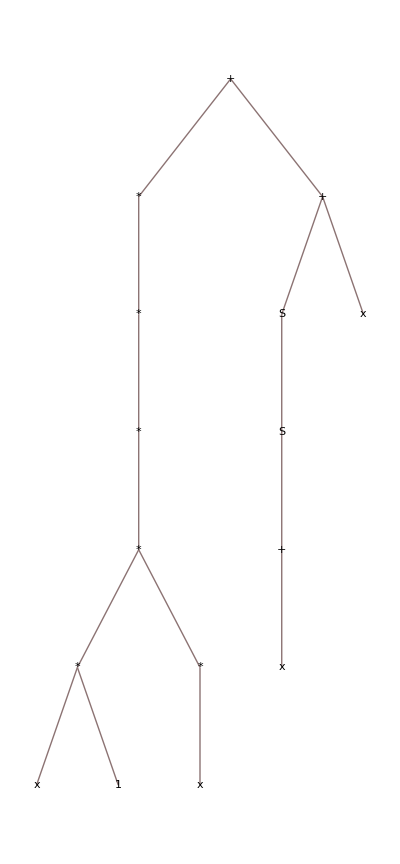
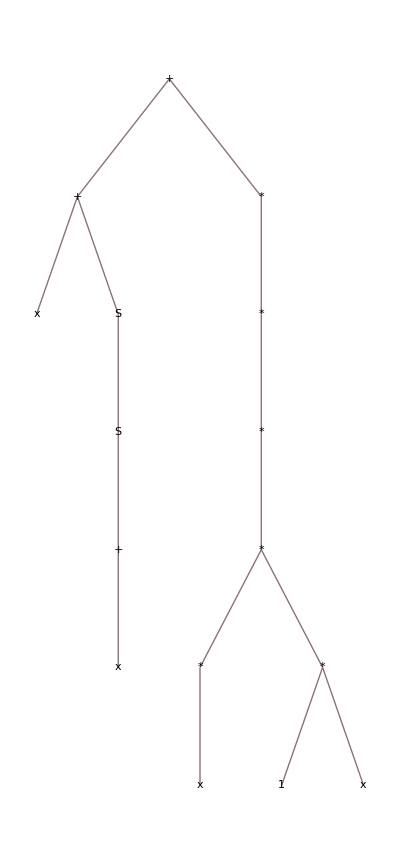
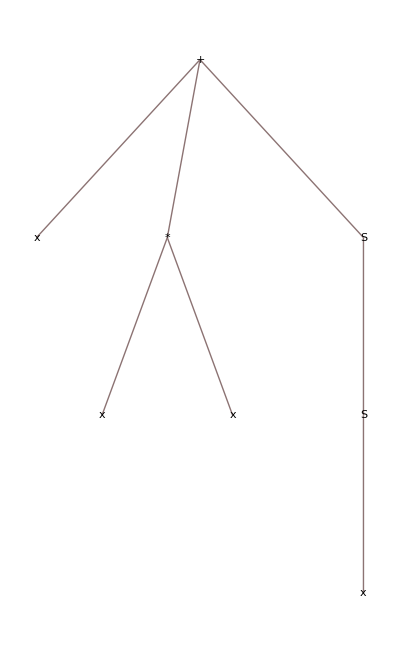
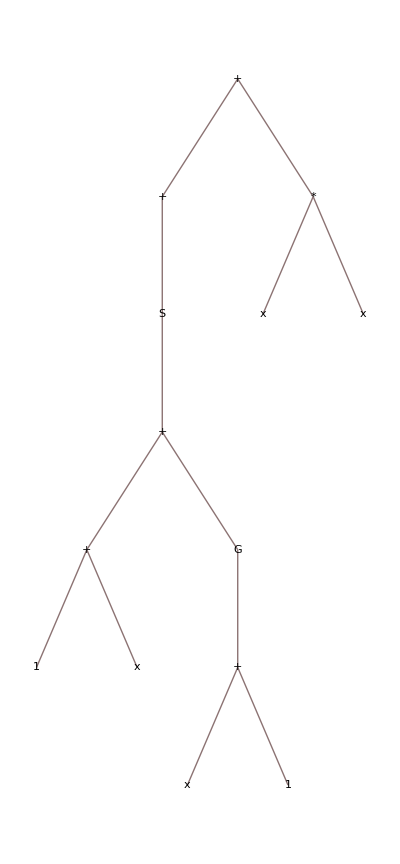
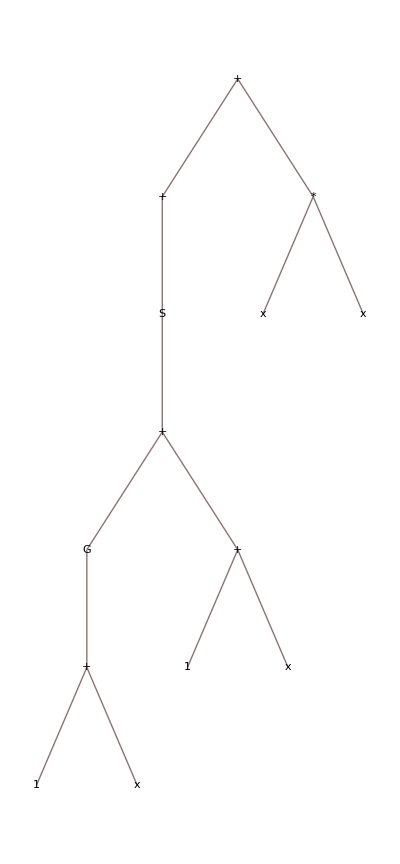
Gen | Genome | Sorted | Simplified | f
last | -Graphics- | -Graphics- | -Graphics- | 0.99656
last | -Graphics- | -Graphics- | -Graphics- | 0.983261
last | -Graphics- | -Graphics- | -Graphics- | 0.978954
last | -Graphics- | -Graphics- | -Graphics- | 0.978529
last | -Graphics- | -Graphics- | -Graphics- | 0.957386
last | -Graphics- | -Graphics- | -Graphics- | 0.956843
last | -Graphics- | -Graphics- | -Graphics- | 0.952837
last | -Graphics- | -Graphics- | -Graphics- | 0.951168
last | -Graphics- | -Graphics- | -Graphics- | 0.940757
last | -Graphics- | -Graphics- | -Graphics- | 0.852304

```mathematica
(res=sortConfigurationResults[sortedData,"A","BSF",10,Output->"BSFGenomes"]/.{x0->x})
```

```mathematica
Export["GP_H2.pdf",%]
```

GP_H2.pdf